```mathematica
data=Import[filenames[[7]]];
```

Part::partd: Part specification filenames⟦7⟧ is longer than depth of object.

Import::chtype: First argument filenames⟦7⟧ is not a valid file, directory, or URL specification.

```mathematica
funcs=Table[PDF[BetaDistribution[n-1,2],x/1000]/1000,{n,2,5}];
```

```mathematica
funcs
```

{Piecewise[{{2 (1-x/1000), 0<x/1000<1}, {0, True}}]/1000,Piecewise[{{3/500 (1-x/1000) x, 0<x/1000<1}, {0, True}}]/1000,Piecewise[{{(3 (1-x/1000) x^2)/250000, 0<x/1000<1}, {0, True}}]/1000,Piecewise[{{((1-x/1000) x^3)/50000000, 0<x/1000<1}, {0, True}}]/1000}

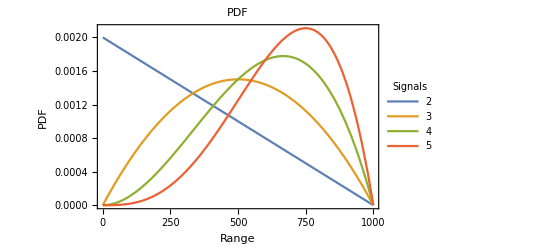

```mathematica
precMargs=Plot[funcs,{x,0,1000},PlotLegends->LineLegend[{"2","3","4","5"},LegendLabel->"Signals"],Frame->{{True,False},{True,False}},FrameLabel->{{"PDF",None},{"Range",None}},PlotLabel->"PDF", PlotRangePadding->0]
```

```mathematica
Export[NotebookDirectory[]<>"text/chapter_4/figures/precision_marginals.jpg",precMargs,ImageResolution->150]
```

/home/kajames/Dropbox/Dissertation/text/chapter_4/figures/precision_marginals.jpg

```mathematica
n=4;
margs=Table[PDF[BetaDistribution[n-1,2],x],{x,0,1,1/100}];
margs[[1]]=2;
xs=(Range[101]-1)*10;
precMarg=Thread[{xs,margs}];
precMarg[[All,2]]/=1000;
```

```mathematica
joint=Flatten[Table[
{prec,pdf}=res;
{prec,mid,If[Abs[mid]≤500-prec/2&&1000-prec>0,pdf/(1000-prec),0]},{mid,-500,500,10},{res,precMarg}
],1];
```

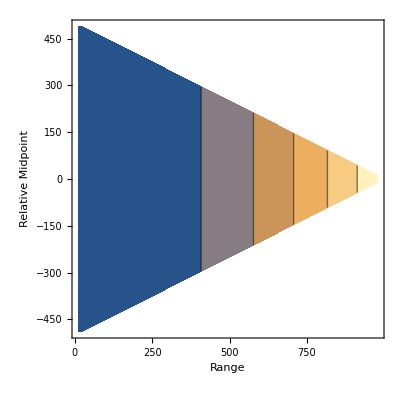

-Graphics3D-

```mathematica
cont=ListContourPlot[joint/.(0->""),PlotRange->All,PlotRangePadding->0, LabelStyle->14, FrameLabel->{"Range","Relative Midpoint"}]
ListPlot3D[joint,PlotRange->All]
```

```mathematica
Export[NotebookDirectory[]<>"text/chapter_4/figures/contour_3_signals.jpg",cont,ImageResolution->100]
```

/home/kajames/Dropbox/Dissertation/text/chapter_4/figures/contour_3_signals.jpg

```mathematica
precMarg
```

{{0,0},{10,1/50000},{20,1/25000},{30,3/50000},{40,1/12500},{50,1/10000},{60,3/25000},{70,7/50000},{80,1/6250},{90,9/50000},{100,1/5000},{110,11/50000},{120,3/12500},{130,13/50000},{140,7/25000},{150,3/10000},{160,1/3125},{170,17/50000},{180,9/25000},{190,19/50000},{200,1/2500},{210,21/50000},{220,11/25000},{230,23/50000},{240,3/6250},{250,1/2000},{260,13/25000},{270,27/50000},{280,7/12500},{290,29/50000},{300,3/5000},{310,31/50000},{320,2/3125},{330,33/50000},{340,17/25000},{350,7/10000},{360,9/12500},{370,37/50000},{380,19/25000},{390,39/50000},{400,1/1250},{410,41/50000},{420,21/25000},{430,43/50000},{440,11/12500},{450,9/10000},{460,23/25000},{470,47/50000},{480,3/3125},{490,49/50000},{500,1/1000},{510,51/50000},{520,13/12500},{530,53/50000},{540,27/25000},{550,11/10000},{560,7/6250},{570,57/50000},{580,29/25000},{590,59/50000},{600,3/2500},{610,61/50000},{620,31/25000},{630,63/50000},{640,4/3125},{650,13/10000},{660,33/25000},{670,67/50000},{680,17/12500},{690,69/50000},{700,7/5000},{710,71/50000},{720,9/6250},{730,73/50000},{740,37/25000},{750,3/2000},{760,19/12500},{770,77/50000},{780,39/25000},{790,79/50000},{800,1/625},{810,81/50000},{820,41/25000},{830,83/50000},{840,21/12500},{850,17/10000},{860,43/25000},{870,87/50000},{880,11/6250},{890,89/50000},{900,9/5000},{910,91/50000},{920,23/12500},{930,93/50000},{940,47/25000},{950,19/10000},{960,6/3125},{970,97/50000},{980,49/25000},{990,99/50000},{1000,1/500}}

```mathematica
Integrate[u^(r-1)*(1-u-w)^(n-s),{u,0,(1-w)}]
```

ConditionalExpression[((1-w)^(5+r-s) Gamma[r] Gamma[6-s])/Gamma[6+r-s],Re[w]<1&&Im[w]==0&&Re[s]<6&&Re[r]>0]

```mathematica
filenames = FileNames["~/Dropbox/Dissertation/presentation/SubjectData*.csv"];
```

```mathematica
ReadFile[filename_,id_]:=Module[{data,headers},
data=Import[filename];
If[Length[data]==6,
data=StringSplit[data[[6,1]],"}"][[2]];
data=StringSplit[#,","]&/@StringSplit[data,"\n"];
data=PadRight[#,Length[data[[1]]],""]&/@data;
];
headers=data[[1]];
data=AssociationThread[headers->#]&/@Rest[data];
Do[
data[[i]][["SubjectId"]]=ToExpression[data[[i,"SubjectId"]]]+100*id;
data[[i]][["GroupId"]]=ToExpression[data[[i,"GroupId"]]]+100*id;
,{i,1,Length[data]}
];
data
];
```

```mathematica
allResults=ParallelTable[ReadFile[filenames[[i]],i],{i,1,Length[filenames]}];
allResults=Flatten[allResults,1];
```

```mathematica
Counts[allResults[[All,"MessageType"]]]
```

<|ClientCompletedStage→10752,PurchaseSignal→4320,Bid→82717,StopBidding→1657,ClockResult→2160,FirstPriceResult→2160|>

```mathematica
fpRes=Select[allResults,#MessageType=="FirstPriceResult"&];
```

```mathematica
fpRes[[1]]
```

<|TimeReceived→2/8/2018 2:14:55 PM,TimeElapsed→00:00:36.7510000,Period→1,SubjectId→201,GroupId→200,MessageType→FirstPriceResult,PlayerIdx→0,WasIgnored→,Institution→FirstPrice,SignalCost→10,SignalsPurchased→1,TotalSignalCost→10,ExpectedValue→1462,RationalLowerBound→962,RationalUpperBound→1962,ActualValue→1145,MyBid→1000,BiddingProfit→0,DiffFromExpected→462,WinnerIdx→2,WonItem→False,WinningBid→1650,SecondHighestBid→1250,TotalProfit→-10,DropOutPrice→,Signal1→1462,Signal2→,Signal3→,Signal4→,Signal5→|>

```mathematica
Length[fpRes]
```

2160

```mathematica
fpRes[[10]]["RationalLowerBound"]
```

3184

```mathematica
goodData=Select[fpRes,ToExpression[#RationalLowerBound]>1000&&ToExpression[#RationalUpperBound]<9000&];
```

```mathematica
goodLosers=Select[goodData,#WonItem=="False"&];
goodWinners=Select[goodData,#WonItem=="True"&];
```

```mathematica
precs=1000-(ToExpression/@Lookup[goodLosers,"RationalUpperBound"]-ToExpression/@Lookup[goodLosers,"RationalLowerBound"]);
discounts=(ToExpression/@Lookup[goodLosers,"MyBid"]-ToExpression/@Lookup[goodLosers,"ExpectedValue"]);
```

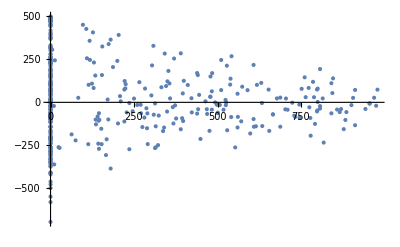

```mathematica
ListPlot[Thread[{precs,discounts}]]
```

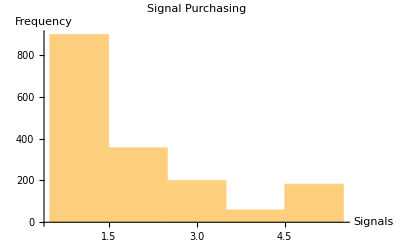

```mathematica
Histogram[ToExpression/@Lookup[goodData,"SignalsPurchased"],AxesLabel->{"Signals","Frequency"}, PlotLabel->"Signal Purchasing"]
```

```mathematica
res=Lookup[#,"SignalsPurchased"]&/@GroupBy[goodData,#Period&];
```

```mathematica
res
```

<|1→{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},2→{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1},3→{5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5},4→{5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5},5→{3,3,4,2,4,2,1,3,3,5,1,1,5,1,5,3,1,3,3,1,4,3,2,5,3,2,3,5,4,3,1,3,1,2,1,1,1,1,1,1,1,3,1,5,1,1,1,3,3,3,3,1,4,2,1,1},6→{5,5,3,1,2,3,3,5,3,1,3,3,5,5,1,1,3,1,1,3,4,3,3,2,3,2,1,3,1,4,1,3,3,2,2,4,1,1,2,1,3,1,1},7→{3,2,1,2,2,2,4,2,1,2,3,2,2,5,1,2,1,3,1,3,2,1,3,1,3,2,3,3,3,1,2,3,2,3,1,1,2,1,1,1,1,2,3,1,3,3,1,2,1,1,3,2},8→{3,1,3,3,2,2,1,5,2,1,1,2,3,1,5,1,1,3,5,3,2,2,5,1,2,2,2,3,1,3,3,1,3,1,2,1,2,3,1,1,1,2,2,3,3,3,2,2,1},9→{2,2,2,3,3,2,1,1,1,2,1,1,2,1,5,1,2,1,3,2,1,1,1,1,1,5,3,3,2,2,2,3,1,1,1,1,4,2,1,2,3,1},10→{1,2,2,1,1,2,2,3,1,3,5,2,3,1,1,2,1,2,1,2,1,3,1,5,2,3,1,5,1,2,1,1,3,1,1,5,4,5,1,1,4,2,1,1,4,5,1,4,1,3,1,1},11→{2,3,3,1,3,4,3,5,3,1,2,2,2,2,1,2,2,1,1,1,1,3,2,2,3,4,2,4,1,2,1,1,2,5,1,2,5,2,1,2,3,2,4,4},12→{1,2,2,4,2,1,1,5,2,1,1,1,1,1,1,1,1,1,2,2,2,2,1,1,3,2,1,1,1,2,1,3,1,5,1,3,4,1,1,2,1,2,1,2,3,2},13→{3,3,2,2,3,2,1,2,3,4,3,1,1,4,1,1,1,2,2,1,3,2,5,1,3,3,1,2,1,2,1,3,1,1,1,1,1,1,1,1,1,1,2,1,5,1,2,1,1,4,2},14→{2,4,2,2,5,2,1,2,4,5,2,1,3,1,2,2,1,1,1,1,1,2,1,2,1,2,1,1,2,3,1,1,1,4,1,1,1,2,1,1,2,1,1,3,1,1,2,2},15→{3,2,1,3,2,2,1,3,1,1,1,3,1,1,1,1,1,1,1,2,1,1,1,3,1,3,1,3,1,1,2,1,1,2,2,2,3,1,3,1,2,1},16→{1,2,3,3,3,1,2,1,3,2,2,1,1,1,1,1,1,1,1,1,2,1,2,1,2,2,3,1,1,1,1,2,1,1,1,1,1,1,1,1,1,3,4,2,4,1,2,1,1,1,2,1,1},17→{4,1,2,2,2,3,1,3,2,2,1,1,1,2,1,3,2,1,2,2,1,2,1,1,1,1,1,1,1,2,1,3,1,1,1,1,1,1,1,1,1,3,1,2,2,1,2,3},18→{3,3,1,2,1,1,3,1,1,1,2,1,1,1,2,3,2,1,2,1,1,1,2,1,1,1,3,1,1,4,1,1,2,1,4,2},19→{2,2,3,1,2,2,1,3,2,1,1,2,1,5,1,3,1,2,1,1,5,3,1,1,2,3,1,1,1,5,1,1,1,1,1,1,1,1,1,1,1,1,2,4,1,1,1,2,1,1,1,2},20→{2,2,2,1,2,2,5,2,2,5,1,2,2,2,1,1,3,2,1,1,5,4,1,1,5,1,1,1,5,1,2,2,1,1,2,1,3,1,1,1,1,2},21→{3,5,2,3,2,4,1,1,2,1,1,1,2,3,2,2,2,2,1,1,1,2,2,1,1,1,1,3,5,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,2,1},22→{2,2,3,2,5,1,1,5,1,2,3,1,3,2,1,1,1,1,2,5,1,1,3,1,2,1,2,1,1,1,2,2,1,1,1,5,1,1,1,1,1,1,1,1,2,1,1,2,2,1,2,2,1},23→{5,2,3,2,1,5,2,2,5,1,2,3,1,1,2,2,1,1,4,1,1,1,2,1,2,1,1,1,2,1,1,1,1,2,1,4,1,1,1,2,1,1,1,1,1,2,1,1,1,1,1,1,1,1,2,2},24→{3,1,3,2,2,5,2,4,5,2,1,1,1,1,1,2,1,1,1,1,1,1,1,1,4,1,1,1,1,1},25→{2,4,5,2,1,4,1,5,5,2,1,1,2,3,1,5,2,2,1,1,1,1,2,1,1,1,2,1,1,2,1,1,1,1,1,2,1,1,1,1,1,1,1,2,1,1,3,1,1,1,1,1},26→{5,1,1,3,2,3,1,3,2,2,1,5,2,1,1,1,2,4,1,1,1,1,2,1,1,1,2,2,1,1,1,1,3,3,1,1,1,2,1,4,1,1,1,3,1,1,3},27→{1,2,1,5,2,2,2,5,1,3,1,2,1,1,5,1,1,1,1,2,5,1,2,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,3,4,1,1,1,1,1,1,1,2,1,1,1,4,3,1,1},28→{2,2,1,1,3,2,2,3,2,2,1,5,1,1,2,1,2,1,1,1,1,2,1,1,2,1,2,4,1,1,2,1,1,1,1,1,1,1,1,3,1,2,1,3},29→{3,3,2,1,1,5,2,1,3,2,5,2,1,1,1,2,1,1,2,1,1,3,1,1,3,1,1,4,2,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1},30→{1,5,1,2,4,2,2,1,1,1,3,1,1,1,3,1,1,1,2,2,2,1,1,1,1,2,1,3,1,1,1,3,1,1,5,2,1,1,1,1,2,1,2,4,1,4,1,1},31→{2,3,1,3,1,1,1,5,1,1,2,1,2,1,1,1,2,1,2,1,1,2,3,1,3,1,1,1,1,1,1,1,1,1,1,4,2,3,1,1,1,2},32→{3,2,2,1,5,1,1,1,2,3,2,1,1,1,1,1,2,2,1,1,1,5,1,2,1,2,4,1,1,1,1,1,1,2,1,5,1,1,3,1},33→{5,1,1,2,5,1,3,1,2,1,1,2,2,1,3,3,1,4,1,3,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,5,3,2,1,2,1,1,1,1},34→{1,2,1,3,4,4,1,5,1,1,2,1,5,1,1,5,1,2,1,1,2,1,2,2,5,3,1,1,2,1,3,2,1,1,1,1,1,2,1,4,1,1,1,5},35→{2,3,2,4,1,1,1,5,3,1,1,2,2,2,1,1,1,2,1,3,1,4,1,1,1,1,1,1,2,1,1,3,3,2,2,1,1,1,1,1,1,1,1,1,1,1,1,3,1,5,1,1,5,1,1,2,1,1,1},36→{1,1,3,3,1,1,1,2,5,1,1,1,4,1,1,3,1,2,2,3,2,1,1,3,2,1,1,1,2,1,2,1,1,3,2,2,1,1,1,1,1,3,5,1,1,2,1}|>

```mathematica
N[Mean/@Map[ToExpression,Table[res[ToString[i]],{i,5,36}],{-1}]]
```

{2.41071,2.51163,2.03846,2.20408,1.90476,2.17308,2.34091,1.78261,1.92157,1.8125,1.64286,1.56604,1.60417,1.66667,1.69231,2.,1.69565,1.73585,1.66071,1.76667,1.71154,1.78723,1.67273,1.63636,1.63265,1.72917,1.59524,1.75,1.72727,2.,1.67797,1.74468}

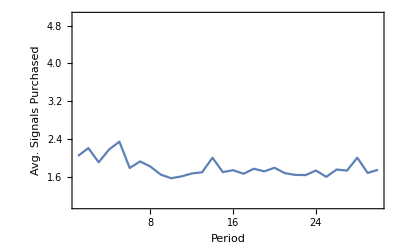

```mathematica
signalPurchasing=ListLinePlot[N[Mean/@Map[ToExpression,Table[res[ToString[i]],{i,7,36}],{-1}]],PlotRangePadding->0,PlotRange->{{1,30},{1,5}},LabelStyle->14,Frame->{{True, False},{True,False}},FrameLabel->{"Period","Avg. Signals Purchased"}]
```

```mathematica
Export[NotebookDirectory[]<>"text/chapter_4/figures/signal_purchasing.jpg",signalPurchasing,ImageResolution->100]
```

/home/kajames/Dropbox/Dissertation/text/chapter_4/figures/signal_purchasing.jpg

```mathematica
goodData[[1]]
```

<|TimeReceived→2/8/2018 2:15:13 PM,TimeElapsed→00:00:54.7976000,Period→1,SubjectId→206,GroupId→202,MessageType→FirstPriceResult,PlayerIdx→0,WasIgnored→,Institution→FirstPrice,SignalCost→10,SignalsPurchased→1,TotalSignalCost→10,ExpectedValue→4146,RationalLowerBound→3646,RationalUpperBound→4646,ActualValue→4039,MyBid→3850,BiddingProfit→0,DiffFromExpected→296,WinnerIdx→3,WonItem→False,WinningBid→4000,SecondHighestBid→3850,TotalProfit→-10,DropOutPrice→,Signal1→4146,Signal2→,Signal3→,Signal4→,Signal5→|>

```mathematica
Counts[ToExpression/@Lookup[goodWinners,"SignalsPurchased"]]
```

<|1→213,5→42,2→91,3→47,4→27|>

```mathematica
resBySignal=Values[KeySort[GroupBy[goodWinners,#SignalsPurchased&]]];
```

```mathematica
N@Mean[ToExpression/@#[[All,"TotalProfit"]]]&/@resBySignal
```

{-278.263,-162.571,-133.702,-120.111,-144.714}

```mathematica
{-278.26291079812205,-162.57142857142858,-133.70212765957447,-120.11111111111111,-144.71428571428572}
```

```mathematica
winners=Select[fpRes,#WonItem=="True"&];
```

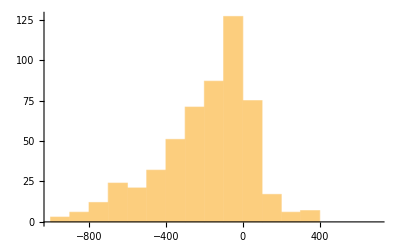

```mathematica
Histogram[ToExpression/@Lookup[winners,"BiddingProfit"]]
```

```mathematica
res=Table[
d=OrderDistribution[{UniformDistribution[{-500,500}],n},{1,n}];
d2=TransformedDistribution[(u+v)/2,{u,v}\[Distributed]d];
ParallelTable[PDF[d2,x],{x,-500,500,10}]
,{n,2,5}
];
```

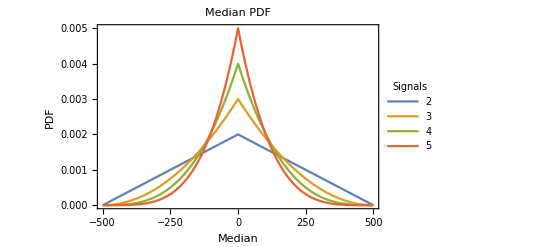

```mathematica
res2=Transpose[{Range[-500,500,10],#}]&/@res;
medianMargs=ListLinePlot[res2,
PlotLegends->LineLegend[{"2","3","4","5"},LegendLabel->"Signals"],Frame->{{True,False},{True,False}},FrameLabel->{{"PDF",None},{"Median",None}},PlotLabel->"Median PDF", PlotRangePadding->0]
```

```mathematica
Export[NotebookDirectory[]<>"text/chapter_4/figures/median_marginals.jpg",medianMargs,ImageResolution->150]
```

/home/kajames/Dropbox/Dissertation/text/chapter_4/figures/median_marginals.jpg

```mathematica
Plot3D[PDF[d,{x,y}],{x,-500,500},{y,-500,500}]
```

-Graphics3D-

1/250

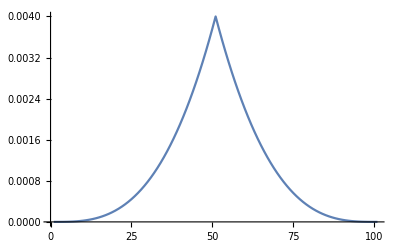

```mathematica
PDF[d2,0]
```

```mathematica
n=5;
ϵ=500;
Integrate[n!/((2ϵ)^n)*(v-u)^(n-2)/((n-2)!),{v,-ϵ,ϵ},{u,-ϵ,v}]
```

1

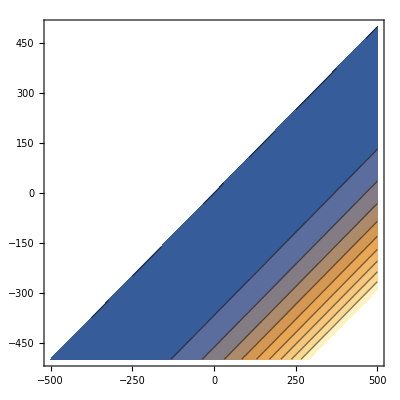

```mathematica
ContourPlot[n!/((2ϵ)^n)*(v-u)^(n-2)/((n-2)!),{v,-ϵ,ϵ},{u,-ϵ,v}]
```

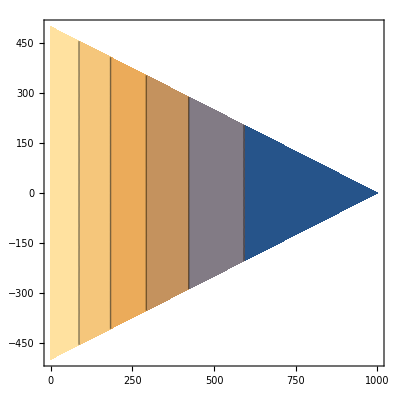

```mathematica
n=4;
ContourPlot[n!/((2ϵ)^n)*(2ϵ-w)^(n-2)/((n-2)!),{w,0,2ϵ},{z,-(2ϵ-w)/2,(2ϵ-w)/2}]
```